```mathematica
RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

656

656

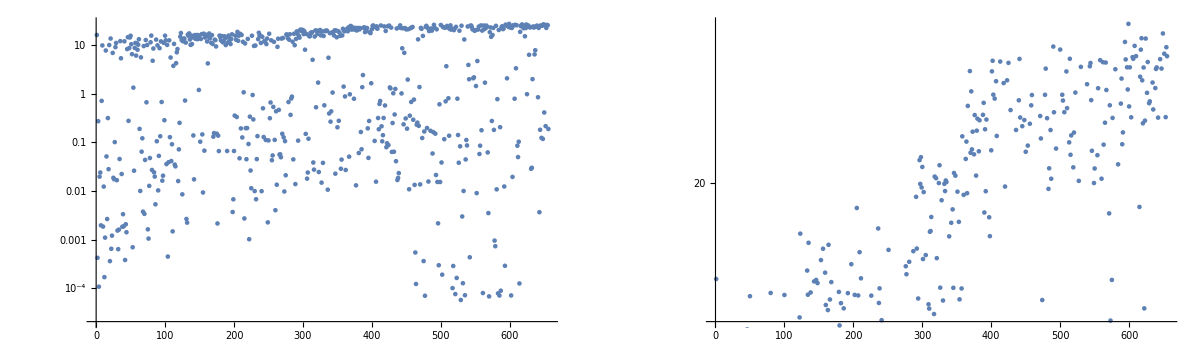

```mathematica
GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{15.,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L0BPhaseSet : -8.2778471843
L1PhaseSet : -18.9797161719
L2PhaseSet : -39.8925716947
L3PhaseSet : 6.2781076785
S1EL_xOffset : 0.0023994869
S1EL_yOffset : -0.000075932
S2EL_xOffset : -0.003089762
S2EL_yOffset : -0.0004405108
S2ER_xOffset : -0.0008619506
S2ER_yOffset : 0.003332619
S1ER_xOffset : 0.0039510076
S1ER_yOffset : 0.0021915268
PDrive_mean_x : 0.0002603931
PDrive_mean_y : -0.0001293509
PDrive_sigma_x : 0.0000442879
PDrive_sigma_y : 0.0000324907
PDrive_mean_xp : -0.0005590112
PDrive_mean_yp : 0.0001791808
PDrive_median_x : 0.0002581005
PDrive_median_y : -0.000130474
PDrive_median_xp : -0.0004949324
PDrive_median_yp : 0.0001757029
PDrive_sigmaSI90_x : 0.0000320279
PDrive_sigmaSI90_y : 0.000029672
PDrive_sigmaSI90_z : 0.0000310156
PDrive_emitSI90_x : 0.0001441559
PDrive_emitSI90_y : 0.0000563283
PDrive_zCentroid : 991.3316820434
PWitness_mean_x : 0.0002378696
PWitness_mean_y : -0.0000307904
PWitness_sigma_x : 0.0000370623
PWitness_sigma_y : 0.0000346167
PWitness_mean_xp : -0.0010250564
PWitness_mean_yp : 0.000484579
PWitness_median_x : 0.0002455432
PWitness_median_y : -0.000028685
PWitness_median_xp : -0.0010286242
PWitness_median_yp : 0.0004898547
PWitness_sigmaSI90_x : 0.0000320262
PWitness_sigmaSI90_y : 0.0000297374
PWitness_sigmaSI90_z : 0.0000135166
PWitness_emitSI90_x : 0.0000438499
PWitness_emitSI90_y : 6.5392e-6
PWitness_zCentroid : 991.3318725314
bunchSpacing : 0.000190488
transverseCentroidOffset : 0.0001011013
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.2159354344
maximizeMe : 27.7860834535

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.000101101

## Plot all

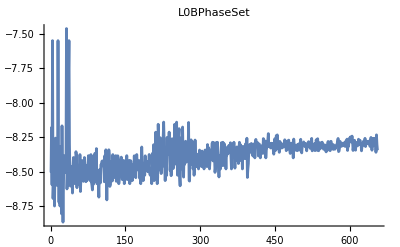
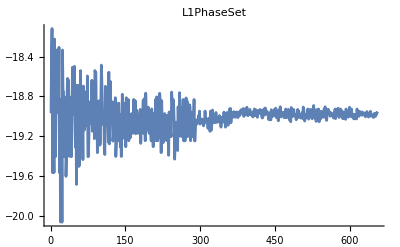
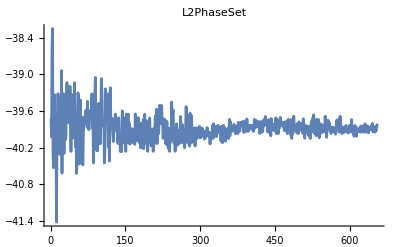
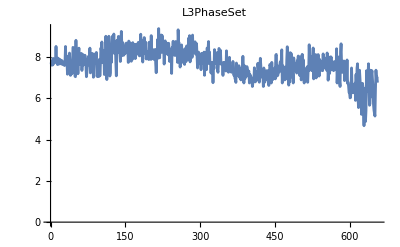
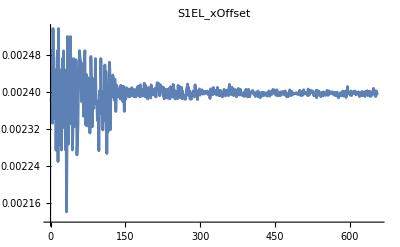
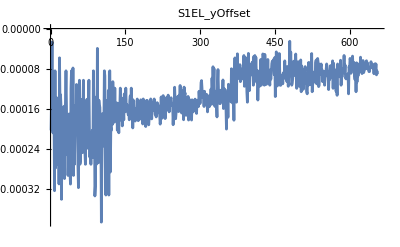
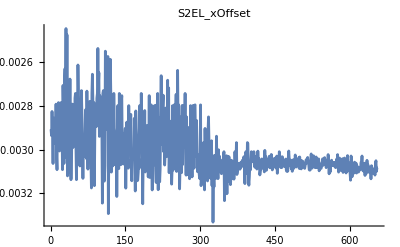
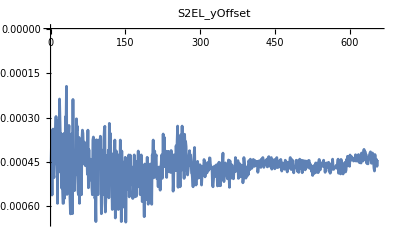
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset}

```mathematica
fitVar = "PDrive_sigmaSI90_z"
fitVar = "bunchSpacing"
```

PDrive_sigmaSI90_z

bunchSpacing

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

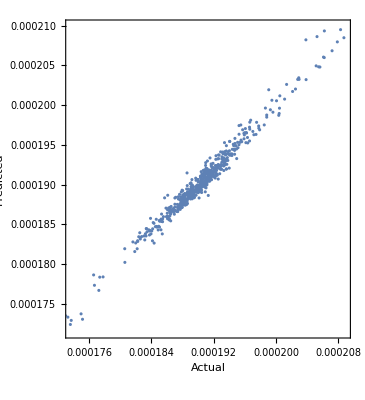

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-750.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1121.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1524.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 3.57837×10^-10 | 3.57837×10^-10 | 148.714 | 6.42811×10^-31
L1PhaseSet | 1 | 1.42629×10^-8 | 1.42629×10^-8 | 5927.52 | 0.
L2PhaseSet | 1 | 4.85037×10^-8 | 4.85037×10^-8 | 20157.7 | 0.
L3PhaseSet | 1 | 2.61436×10^-9 | 2.61436×10^-9 | 1086.5 | 2.79592×10^-140
S1ELxOffset | 1 | 2.84471×10^-10 | 2.84471×10^-10 | 118.223 | 2.14866×10^-25
S1ELyOffset | 1 | 1.24058×10^-9 | 1.24058×10^-9 | 515.571 | 2.89329×10^-84
S1ERxOffset | 1 | 1.73969×10^-7 | 1.73969×10^-7 | 72300. | 0.
S1ERyOffset | 1 | 2.41558×10^-13 | 2.41558×10^-13 | 0.100389 | 0.751466
S2ELxOffset | 1 | 4.22764×10^-10 | 4.22764×10^-10 | 175.697 | 1.25954×10^-35
S2ELyOffset | 1 | 3.40497×10^-10 | 3.40497×10^-10 | 141.507 | 1.24023×10^-29
S2ERxOffset | 1 | 1.77505×10^-9 | 1.77505×10^-9 | 737.695 | 8.54264×10^-109
S2ERyOffset | 1 | 2.52578×10^-11 | 2.52578×10^-11 | 10.4969 | 0.0012574
Error | 643 | 1.5472×10^-9 | 2.40622×10^-12 |  | 
Total | 655 | 2.45344×10^-7 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | -8.27785 | -6.55681
L1PhaseSet | -20.312 | -18.9797 | 1.33233
L2PhaseSet | -38.6737 | -39.8926 | -1.21887
L3PhaseSet | -1.46329 | 6.27811 | 7.7414
S1EL_xOffset | 0.000385255 | 0.00239949 | 0.00201423
S1EL_yOffset | -0.000241114 | -0.000075932 | 0.000165182
S2EL_xOffset | -0.00141787 | -0.00308976 | -0.0016719
S2EL_yOffset | 0.0000111705 | -0.000440511 | -0.000451681
S2ER_xOffset | -0.00223816 | -0.000861951 | 0.00137621
S2ER_yOffset | -0.000675996 | 0.00333262 | 0.00400862
S1ER_xOffset | 0.00100714 | 0.00395101 | 0.00294387
S1ER_yOffset | 0.000398456 | 0.00219153 | 0.00179307
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]